## From Giulio and Tim:

### General:

```mathematica
WolframLanguageData["Exp","DocumentationExampleInputs"]
```

```mathematica
SyntaxInformation[Exp]
```

### Defined functions:

```mathematica
parseString[str_String]:=FrontEndExecute[FrontEnd`ReparseBoxStructurePacket[str]];
```

```mathematica
flattenParse[exp_]:=Flatten@ReplaceRepeated[exp, RowBox[{anything___}]:>{anything}]
```

```mathematica
SetAttributes[makeExpressionString, {HoldFirst}]
makeExpressionString[exp_]:=StringTake[ToString[HoldComplete[exp], InputForm], {StringLength["HoldComplete["]+1,-StringLength["]"]-1}]
```

## From Giulio regarding parsing:

```mathematica
ClearAll[parseInput,takepart]
```

```mathematica
parseInput[str_String]:=ReplaceAll[Replace[FrontEndExecute[FrontEnd`ReparseBoxStructurePacket[str]],RowBox[x_]:>x,{0,Infinity}]," ":> Nothing];
```

```mathematica
takepart[expr_String,level_Integer]:=Replace[level[parseInput[expr],{level}],x_/;!AtomQ[x]:>Head[x],{1}]
```

```mathematica
good="f[1,g[1,2],3]";
```

```mathematica
bad="f[1,g[1,2,3]";
```

```mathematica
correction1="f[1,g[1,2,3]]";
```

```mathematica
correction2="f[1,g[1,2],3]";
```

```mathematica
Replace[Level[parseInput["Exp[1+2Sin[x]]"],{3}],x_/;!AtomQ[x]:>Head[x],{1}]
```

```mathematica
Replace[Level[parseInput["Exp[1+2Sin[x]]"],{4}],x_/;!AtomQ[x]:>Head[x],{1}][[1]]
```

Sin

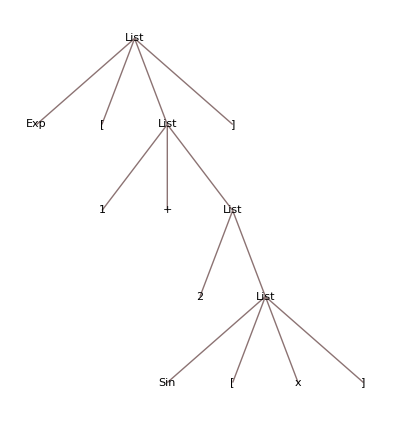

```mathematica
myexpression= parseInput@"Exp[1+2Sin[x]]";myexpression//TreeForm
```

```mathematica
Replace[Level[myexpression,{2}],x_/;!AtomQ[x]:>Head[x],{1}]
```

{Sin,[,x,]}

```mathematica
(* Maybe use with here *)
```

```mathematica
getlevels[n_Integer]:=With[{el=n},Replace[Level[myexpression,{el}],x_/;!AtomQ[x]:>Head[x],{1}]]
```

```mathematica
Thread[getlevels[Range[Depth[myexpression-1]]]]//Column
```

{Exp,[,List,]}
{1,+,List}
{2,List}
{Sin,[,x,]}
{}
{}

## Create simple expression to play with:

Choose an expression, then remove the final bracket for now:

```mathematica
myexpressionstring = "Exp[1+2 Sin[x]]"
```

Exp[1+2 Sin[x]]

```mathematica
myexpressionstring = "Exp[Sin[x]]"
```

```mathematica
bracketpositions=StringPosition[myexpressionstring,"]"]
```

{{14,14},{15,15}}

```mathematica
brackettodrop=bracketpositions[[-1]]
```

```mathematica
mybrokenexpressionstring= StringDrop[myexpressionstring,brackettodrop]
```

```mathematica
flattenParse@parseString[mybrokenexpressionstring]
```

```mathematica
myexpression=DeleteCases[flattenParse@parseString[mybrokenexpressionstring],"  "]
```

```mathematica
myexpression=DeleteCases[flattenParse@parseString[myexpressionstring]," "]
```

{Exp,[,1,+,2,Sin,[,x,],]}

```mathematica
StringJoin[myexpression]
```

Exp[1+2Sin[x]]

```mathematica
parseString[myexpressionstring]
```

```mathematica
myexpression
```

Tim said, that every time a [ is found, go a level down. Try to do that.

Or maybe start with turning the function names from String to objects

```mathematica
positions=Position[myexpression,_?NameQ]//Flatten
```

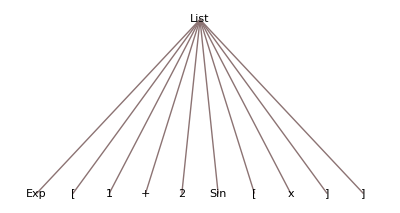

```mathematica
myexpression//TreeForm
```

```mathematica
StringCount[{"1","+","2","Sin","[","x","["},"["]//Total
```

2

```mathematica
StringCases[{"1","+","2","Sin","[","x"},"["]
```

{{},{},{},{},{[},{}}

## Playing with the expression:

```mathematica
myexpression
```

{Exp,[,1,+,2,Sin,[,x,],]}

### Continue with this one:

```mathematica
myexpression/. head_[before___,function_,"["_,body___, "]"_,after___]/;   If[Length[{body}]>0, Echo[{{body},{Total@StringCount[{body},"["],Total@StringCount[{body},"]"]}},"Before:"]]&& Total@StringCount[{body},"["]== Total@StringCount[{body},"]"]  && If[Length[{body}]>0, Echo[{"head:",head,"before:",before,"function:",function,"openbracket:",openbracket,"body:",body,"closebracket:",closebracket,"after:",after},"After:"]]->head[before,function[openbracket,body,closebracket],after]//TreeForm
```

Before: {{1,+,2,Sin,[,x},{1,0}}

Before: {{1,+,2,Sin,[,x,]},{1,1}}

After: {head:,List,before:,function:,Exp,openbracket:,[,body:,1,+,2,Sin,[,x,],closebracket:,],after:}

Before: {{x},{0,0}}

After: {head:,List,before:,Exp,[,1,+,2,function:,Sin,openbracket:,[,body:,x,closebracket:,],after:,]}

Before: {{x,]},{0,1}}

-Graphics-

```mathematica
myexpression//FullForm
```

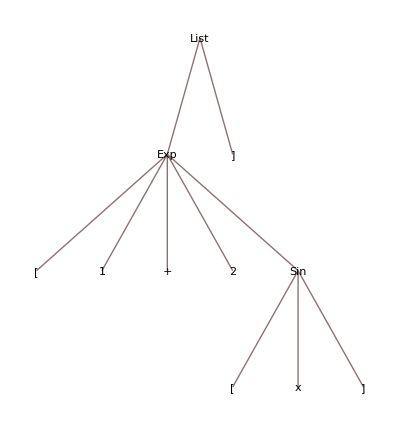

```mathematica
myexpression//. head_[before___,function_,openbracket_,body___,closebracket_,otherclosebracket___,after___]/;openbracket=="[" && closebracket=="]"&& otherclosebracket=="]" ->head[before,function[openbracket,body,closebracket,otherclosebracket],after]//TreeForm
```

```mathematica
myexpression//. {before___,function_String,openbracket_String,body___,closebracket_String,after___}/;openbracket=="[" && closebracket=="]" ->{before, function[openbracket,{body,closebracket}],after}//TreeForm;
```

```mathematica
myexpression//. {before___,function_String,openbracket_String,body___,closebracket_String,after___}/;openbracket=="[" && closebracket=="]" ->{before, function ,{openbracket,body,closebracket},after}//TreeForm;
```

```mathematica
mynewexpression=myexpression/. {function_,openbracket_String,body___,closebracket_String}/;openbracket=="[" && closebracket=="]" ->{ function,{openbracket,body,closebracket}}//TreeForm
```

```mathematica
mynewexpression//. List_Symbol[stuff___] ->stuff //TreeForm
```

```mathematica
Delete[x]
```

## Playing with the reverse expression

```mathematica
myexpressionreversed =Reverse[ myexpression,1]/. item_ /; item== "]" -> "Q"  /. item_/; item=="[" -> "]"/. item_ /; item=="Q" -> "[";
```

```mathematica
myexpressionreversed=myexpression//Reverse;
```

```mathematica
myexpressionreversed //TreeForm
```

```mathematica
myexpressionreversed[[4]]
```

```mathematica
StringCases[myexpressionreversed[[2;;4]],"]"]//Flatten
```

```mathematica
StringContainsQ["StyleBox[\"string\", \"TI\"]",patt]
```

```mathematica
Length@myexpressionreversed[[2;;4]]
```

```mathematica
AnyTrue
```

```mathematica
!AnyTrue[StringContainsQ["]"]]@myexpressionreversed[[2;;4]]
```

```mathematica
myexpression//Reverse//TreeForm
```

```mathematica
ReplaceRepeated[%194, List[{anything___}]:>{anything}]//TreeForm
```

```mathematica
myexpressionreversed//. head_[before___,closebracket_,body___,openbracket_,function_,after___] /;openbracket=="[" && closebracket=="]" &&  NoneTrue[StringContainsQ["]"]]@{body}->head[before,function,{closebracket,body,openbracket},after];
```

```mathematica
%165[[4]]//Head
```

```mathematica
mynewexpressionreversed=myexpressionreversed/. {openbracket_,body___,closebracket_,function_,therest___} /;openbracket=="[" && closebracket=="]" ->{{openbracket,body,closebracket,function},therest};mynewexpressionreversed//TreeForm
```

```mathematica
//. List_Symbol[stuff___] ->stuff;
```

```mathematica
mynewexpressionreversedcleaned = mynewexpressionreversed//.  {openbracket_,body___,closebracket_} /;openbracket=="[" && closebracket=="]" ->body;mynewexpressionreversedcleaned//TreeForm
```

```mathematica
Reverse[mynewexpressionreversed]/.  {_,closebracket_} /;closebracket=="]"  ->555//TreeForm
```

```mathematica
mynewexpressionreversed[[0]]//Head
```

```mathematica
Delete[x]
```

```mathematica
myexpression//TreeForm
```

```mathematica
Reverse[myexpression]//TreeForm
```

## Play with functions:

```mathematica
myexpression//TreeForm
```

-Graphics-

```mathematica
WolframLanguageData["Exp","DocumentationExampleInputs"];
```

```mathematica
SyntaxInformation[Exp][[1,2]]//Length
```

1

```mathematica
[ [ [   ] ] ]
```